```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True
```

True

```mathematica
<<"ErrorBarPlots`"
```

## Neural network approximation of Bessel[1, x]

### Comparison of the root mean square error (or deviation) using the following training and validation sets

#### Training and validation data

```mathematica
dataBessel = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 50000];
validationBessel = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[-8, 8, 0.001];
$refValues=BesselJ[1, $refRange];
$myMetric={};
```

#### Tanh Neural Network for Bessel Function

```mathematica
tanhNet = NetChain[{LinearLayer[30], Tanh, LinearLayer[20], Tanh, LinearLayer[1]}, "Input"->"Real", "Output"->NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

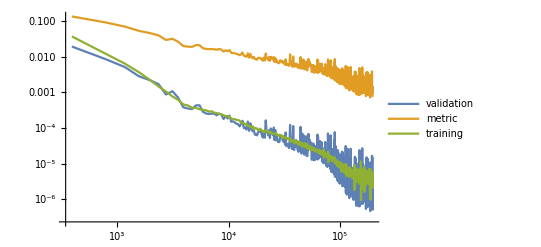

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[besselTanhRMSE, besselTanhMax]
```

```mathematica
besselTanhRMSE ={}; besselTanhMax = {};
```

```mathematica
Table[{trainedTanhNet = NetTrain[tanhNet, dataBessel, ValidationSet->validationBessel, MaxTrainingRounds->100]; AppendTo[besselTanhRMSE,RootMeanSquare[trainedTanhNet[#] - BesselJ[1, #] &@ $refRange]]; AppendTo[besselTanhMax, Max[trainedTanhNet[#] - BesselJ[1, #] &@ $refRange]];Clear[trainedTanhNet]}, 20];
```

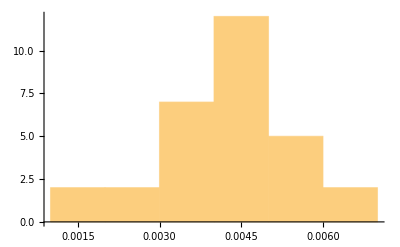

```mathematica
Histogram[besselTanhRMSE]
```

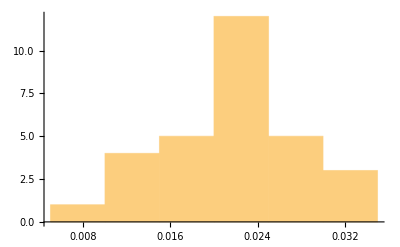

```mathematica
Histogram[besselTanhMax]
```

#### Gaussian Neural Network for Bessel Function

```mathematica
gaussNet = NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^(# ^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^(#^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
Clear[trainedGaussNet]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

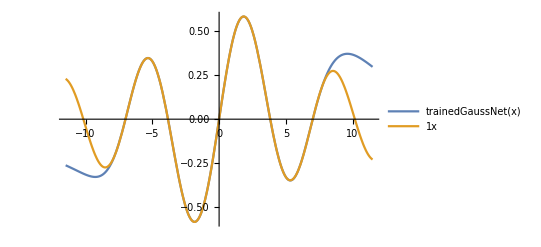

```mathematica
Plot[{trainedGaussNet[x], BesselJ[1, x]}, {x, -11.5, 11.5}, PlotLegends->"Expressions"]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

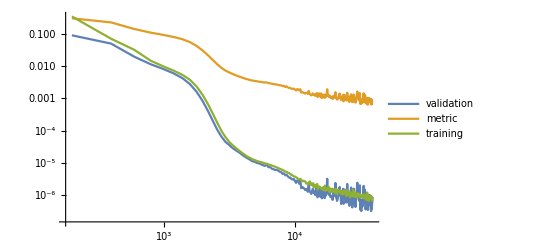

```mathematica
ListLinePlot[{validationLossListG,$myMetric,Transpose[{Range[Length[#]]*validationLossListG[[1,1]],#}& @Mean[Transpose@Partition[batchLossListG,validationLossListG[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[besselGaussRMSE, besselGaussMax]
```

```mathematica
besselGaussRMSE ={}; besselGaussMax = {};
```

```mathematica
Table[{trainedGaussNet = NetTrain[gaussNet, dataBessel, ValidationSet->validationBessel, MaxTrainingRounds->100]; AppendTo[besselGaussRMSE,RootMeanSquare[trainedGaussNet[$refRange] - $refValues]]; AppendTo[besselGaussMax, Max[trainedGaussNet[$refRange] - $refValues]];20];
```

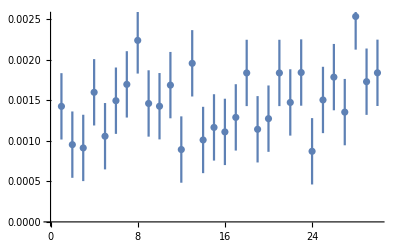

```mathematica
ErrorListPlot[Table[{besselGaussRMSE[[i]], StandardDeviation[besselGaussRMSE]}, {i, 1, Length[besselGaussRMSE]}], ErrorBarFunction -> Automatic]
```

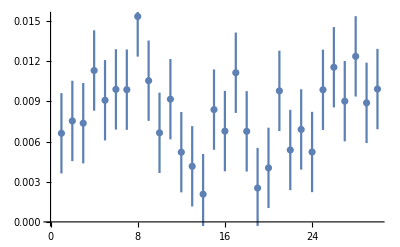

```mathematica
ErrorListPlot[Table[{besselGaussMax[[i]], StandardDeviation[besselGaussMax]}, {i, 1, Length[besselGaussMax]}], ErrorBarFunction -> Automatic]
```

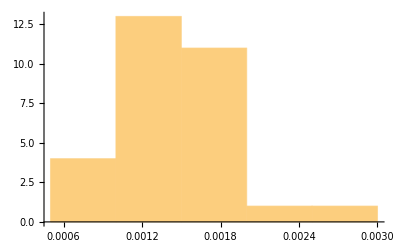

```mathematica
Histogram[besselGaussRMSE]
```

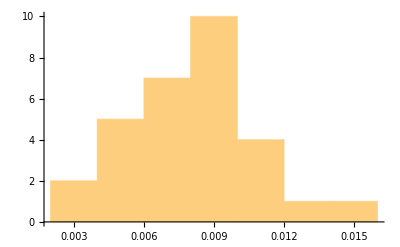

```mathematica
Histogram[besselGaussMax]
```

#### Sinusoidal Neural Network for Bessel function

```mathematica
sinNet = NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSinNet]
```

```mathematica
plotData[points_,color_]:=ListLinePlot[points,PlotStyle->color,FrameTicks->False,PlotRangePadding->0.1,Frame->True,PlotRange->All]
```

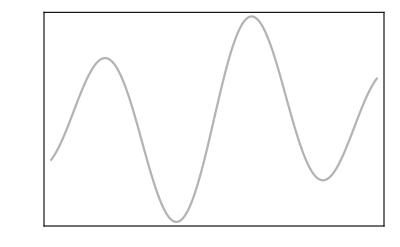

```mathematica
plot=plotData[{$refValues},GrayLevel[0.7]]
```

```mathematica
plotSolution[net_,t_]:=Show[plot,plotData[net@$refRange,Red]]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->50,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

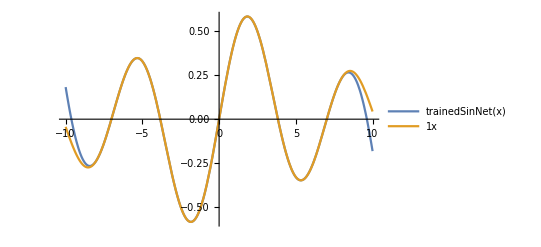

```mathematica
Plot[{trainedSinNet[x], BesselJ[1, x]}, {x, -10, 10}, PlotLegends->Placed["Expressions",{0.8, 0.8}]]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataBessel,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationBessel,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

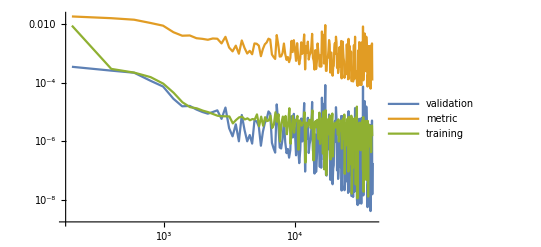

```mathematica
ListLinePlot[{validationLossListS,$myMetric,Transpose[{Range[Length[#]]*validationLossListS[[1,1]],#}& @Mean[Transpose@Partition[batchLossListS,validationLossListS[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[besselSinRMSE, besselSinMax]
```

```mathematica
besselSinRMSE ={}; besselSinMax = {};
```

```mathematica
Table[{trainedSinNet = NetTrain[sinNet, dataBessel, ValidationSet->validationBessel, MaxTrainingRounds->100]; AppendTo[besselSinRMSE,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; AppendTo[besselSinMax, Max[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]];}, 30];
```

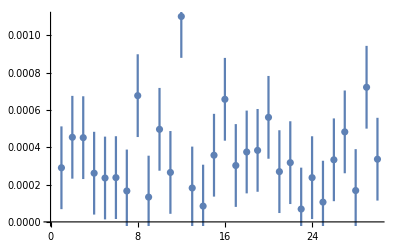

```mathematica
ErrorListPlot[Table[{besselSinRMSE[[i]], StandardDeviation[besselSinRMSE]}, {i, 1, Length[besselSinRMSE]}], ErrorBarFunction -> Automatic]
```

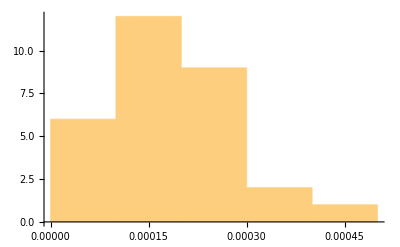

```mathematica
Histogram[besselSinRMSE]
```

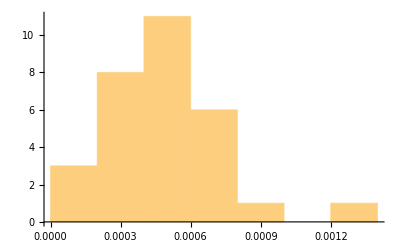

```mathematica
Histogram[besselSinMax]
```

The sinusoidal neural network has the least root mean square error, so we will try to analyse it further.

### Comparison of performance of sinusoidal neural net using varying datasets

```mathematica
dataBessel1 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 10000];
dataBessel3 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 100000];
dataBessel4 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 500000];
dataBessel5 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 1000000];
dataBessel6 = (# -> BesselJ[1, #]) &@ RandomReal[{-8, 8}, 50000];
```

```mathematica
Clear[trainedSinNet, besselSinRMSE1]; besselSinRMSE1 = {};
Table[{trainedSinNet = NetTrain[sinNet, dataBessel1, ValidationSet->validationBessel, MaxTrainingRounds->500]; AppendTo[besselSinRMSE1,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; Clear[trainedSinNet]}, 30];
```

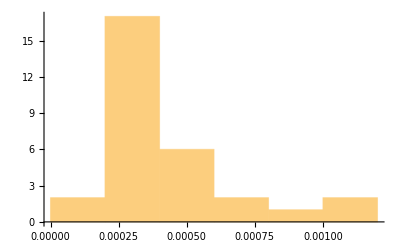

```mathematica
Histogram[besselSinRMSE1]
```

```mathematica
Clear[trainedSinNet, besselSinRMSE2]; besselSinRMSE2 = {};
Table[{trainedSinNet = NetTrain[sinNet, dataBessel6, ValidationSet->validationBessel, MaxTrainingRounds->150]; AppendTo[besselSinRMSE2,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; Clear[trainedSinNet]}, 30];
```

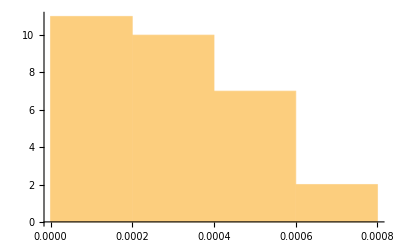

```mathematica
Histogram[besselSinRMSE2]
```

```mathematica
Clear[trainedSinNet, besselSinRMSE3]; besselSinRMSE3 = {};
Table[{trainedSinNet = NetTrain[sinNet, dataBessel3, ValidationSet->validationBessel, MaxTrainingRounds->50]; AppendTo[besselSinRMSE3,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; Clear[trainedSinNet]}, 30];
```

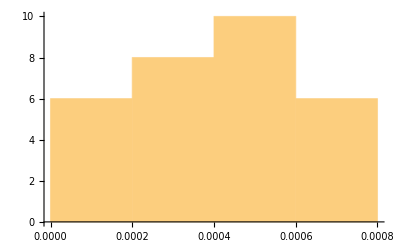

```mathematica
Histogram[besselSinRMSE3]
```

```mathematica
Clear[trainedSinNet, besselSinRMSE4]; besselSinRMSE4 = {};
Table[{trainedSinNet = NetTrain[sinNet, dataBessel4, ValidationSet->validationBessel, MaxTrainingRounds->20]; AppendTo[besselSinRMSE4,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; Clear[trainedSinNet]}, 30];
```

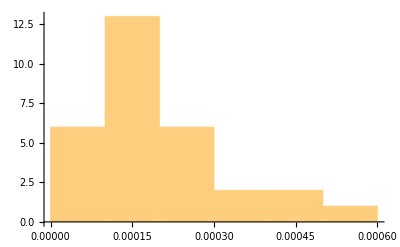

```mathematica
Histogram[besselSinRMSE4]
```

```mathematica
Clear[trainedSinNet, besselSinRMSE5]; besselSinRMSE5 = {};
Table[{trainedSinNet = NetTrain[sinNet, dataBessel5, ValidationSet->validationBessel, MaxTrainingRounds->10]; AppendTo[besselSinRMSE5,RootMeanSquare[trainedSinNet[#] - BesselJ[1, #] &@ $refRange]]; Clear[trainedSinNet]}, 30];
```

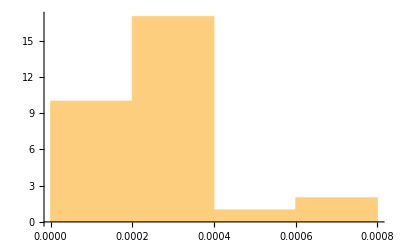

```mathematica
Histogram[besselSinRMSE5]
```

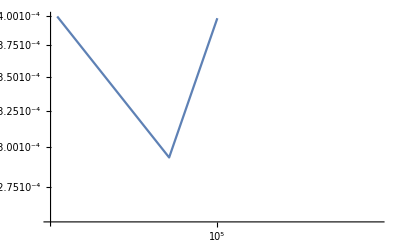

```mathematica
ListLinePlot[{{10000,Mean[besselSinRMSE1]}, {50000,Mean[besselSinRMSE2]}, {100000,Mean[besselSinRMSE3]}, {500000,Mean[besselSinRMSE4]}, {1000000,Mean[besselSinRMSE5]}}, ScalingFunctions->{"Log10", "Log10"}, PlotRange->All]
```

This plot suggests that the error decreases almost exponentially with increasing training data..12

## Neural network approximation of a rational polynomial function

Consider the polynomial 1 + 2x + 3 x^2 + 4 x^3 + 5 x^4 + 6 x^5.

```mathematica
dataRational = (# -> 1 + 2# + 3 #^2 + 4#^3+5#^4+6#^5) &@ RandomReal[{-1, 1}, 100000];
```

```mathematica
validationRational = (# -> 1 + 2# + 3 #^2 + 4#^3+5#^4+6#^5) &@ RandomReal[{-1, 1}, 200];
```

#### My metric

```mathematica
$refRange = Range[-1, 1, 0.001];
$refValues= 1 + 2# + 3 #^2 + 4#^3+5#^4+6#^5 &@ $refRange;
Clear[$myMetric]
$myMetric={};
```

#### Ramp Neural Network for Rational function

```mathematica
rampNet = NetChain[{LinearLayer[30], Ramp, LinearLayer[20], Ramp, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedRampNet, validationLossList, batchLossList]
```

```mathematica
{trainedRampNet,validationLossList,batchLossList}=NetTrain[rampNet, dataRational,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationRational,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

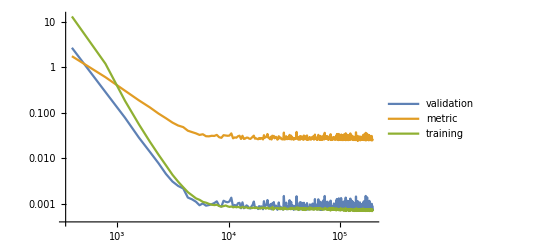

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[rationalRampRMSE, rationalRampMax]
```

```mathematica
rationalRampRMSE ={}; rationalRampMax = {};
```

```mathematica
Table[{trainedRampNet = NetTrain[rampNet, dataRational, ValidationSet->validationRational, MaxTrainingRounds->100]; AppendTo[rationalRampRMSE,RootMeanSquare[trainedRampNet[$refRange] - $refValues]]; AppendTo[rationalRampMax, Max[trainedRampNet[$refRange] - $refValues]];Clear[trainedRampNet]}, 28];
```

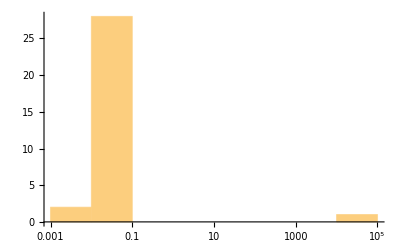

```mathematica
Histogram[rationalRampRMSE, "Log"]
```

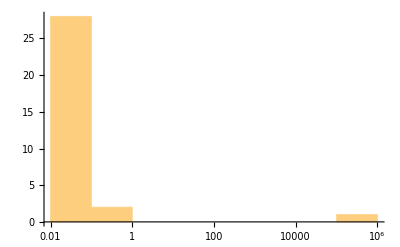

```mathematica
Histogram[rationalRampMax, "Log"]
```

Let .12us now restrict the domain to positive real numbers.

```mathematica
dataRational = (# -> 1 + 2# + 3 #^2 + 4#^3 + 5#^4 + 6#^5) &@ RandomReal[{0, 1}, 100000];
```

```mathematica
validationRational = (# -> 1 + 2# + 3 #^2 + 4#^3 + 5#^4 + 6#^5) &@ RandomReal[{0, 1}, 200];
```

#### My metric

```mathematica
$refRange = Range[0, 1, 0.001];
$refValues= 1 + 2# + 3 #^2 + 4#^3 + 5#^4 + 6#^5 &@ $refRange;
```

```mathematica
Clear[$myMetric]
$myMetric={};
```

```mathematica
Clear[rationalRampRMSE, rationalRampMax]
```

```mathematica
rationalRampRMSE ={}; rationalRampMax = {};
```

```mathematica
Table[{trainedRampNet = NetTrain[rampNet, dataRational, ValidationSet->validationRational, MaxTrainingRounds->50]; AppendTo[rationalRampRMSE,RootMeanSquare[trainedRampNet[$refRange] - $refValues]]; AppendTo[rationalRampMax, Max[trainedRampNet[$refRange] - $refValues]];Clear[trainedRampNet]}, 30];
```

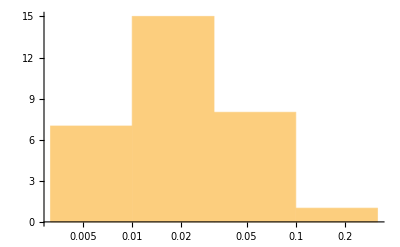

```mathematica
Histogram[rationalRampRMSE, "Log"]
```

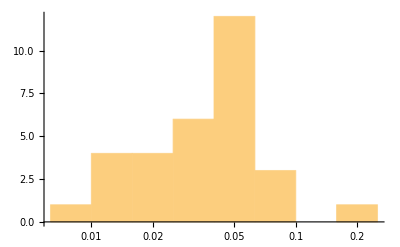

```mathematica
Histogram[rationalRampMax, "Log"]
```

## Neural network approximation of LaguerreL[10,0.5, x]

### Comparison of the root mean square error (or deviation) using the following training and validation sets

#### Training and validation data

```mathematica
dataLaguerre = (# -> LaguerreL[10, 0.5, #]) &@ RandomReal[{0, 8}, 100000];
validationLaguerre = (# -> LaguerreL[10, 0.5, #]) &@ RandomReal[{0, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[0, 8, 0.001];
$refValues=LaguerreL[10, 0.5, $refRange];
```

```mathematica
Clear[$myMetric]
$myMetric={};
```

#### Tanh Neural Network for Laguerre polynomial

```mathematica
tanhNet = NetChain[{LinearLayer[30], Tanh, LinearLayer[20], Tanh, LinearLayer[1]}, "Input"->"Real", "Output"->NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedTanhNet]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataLaguerre,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationLaguerre,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

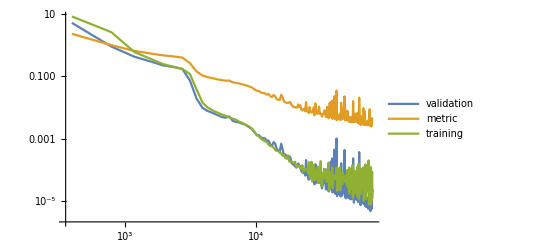

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[laguerreTanhRMSE, laguerreTanhMax]
```

```mathematica
laguerreTanhRMSE ={}; laguerreTanhMax = {};
```

```mathematica
Table[{trainedTanhNet = NetTrain[tanhNet, dataLaguerre, ValidationSet->validationLaguerre, MaxTrainingRounds->100]; AppendTo[laguerreTanhRMSE,RootMeanSquare[trainedTanhNet[$refRange] - $refValues]]; AppendTo[laguerreTanhMax, Max[trainedTanhNet[$refRange] - $refValues]];Clear[trainedTanhNet]}, 30];
```

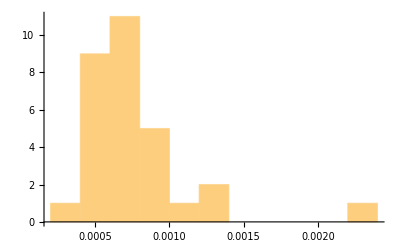

```mathematica
Histogram[laguerreTanhRMSE]
```

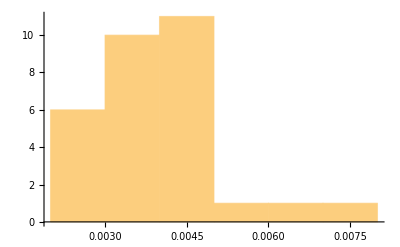

```mathematica
Histogram[laguerreTanhMax]
```

#### Gaussian Neural Network for Laguerre polynomial

```mathematica
gaussNet = NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^(# ^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^(#^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
Clear[trainedGaussNet]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataLaguerre,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationLaguerre,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

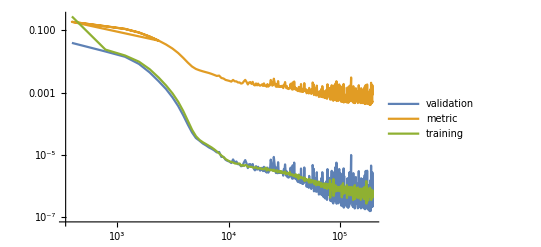

```mathematica
ListLinePlot[{validationLossListG,$myMetric,Transpose[{Range[Length[#]]*validationLossListG[[1,1]],#}& @Mean[Transpose@Partition[batchLossListG,validationLossListG[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[besselGaussRMSE, besselGaussMax]
```

```mathematica
besselGaussRMSE ={}; besselGaussMax = {};
```

```mathematica
Table[{trainedGaussNet = NetTrain[gaussNet, dataBessel, ValidationSet->validationBessel, MaxTrainingRounds->100]; AppendTo[besselGaussRMSE,RootMeanSquare[trainedGaussNet[#] - BesselJ[1, #] &@ $refRange]]; AppendTo[besselGaussMax, Max[trainedGaussNet[#] - BesselJ[1, #] &@ $refRange]];Clear[trainedGaussNet]}, 30];
```

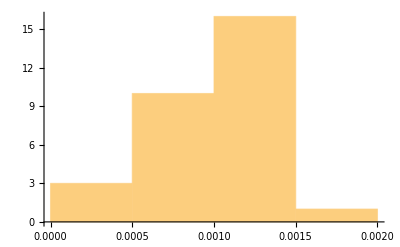

```mathematica
Histogram[besselGaussRMSE]
```

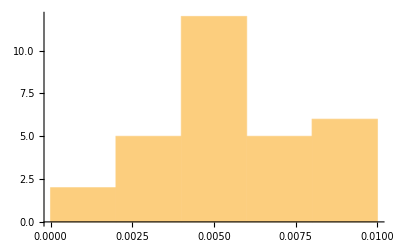

```mathematica
Histogram[besselGaussMax]
```

#### Sinusoidal Neural Network for Laguerre polynomial

```mathematica
sinNet = NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSinNet]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataLaguerre,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationLaguerre,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

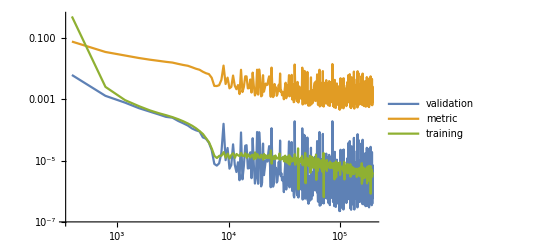

```mathematica
ListLinePlot[{validationLossListS,$myMetric,Transpose[{Range[Length[#]]*validationLossListS[[1,1]],#}& @Mean[Transpose@Partition[batchLossListS,validationLossListS[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[laguerreSinRMSE, laguerreSinMax]
```

```mathematica
laguerreSinRMSE ={}; laguerreSinMax = {};
```

```mathematica
Table[{trainedSinNet = NetTrain[sinNet, dataLaguerre, ValidationSet->validationLaguerre, MaxTrainingRounds->100]; AppendTo[laguerreSinRMSE,RootMeanSquare[trainedSinNet[$refRange] - $refValues]]; AppendTo[laguerreSinMax, Max[trainedSinNet[$refRange] - $refValues]];Clear[trainedSinNet]}, 30];
```

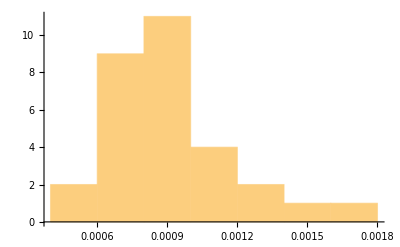

```mathematica
Histogram[laguerreSinRMSE]
```

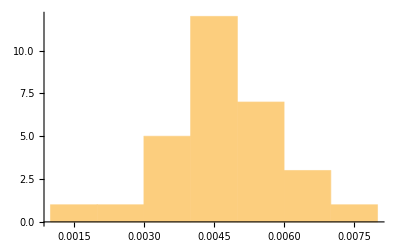

```mathematica
Histogram[laguerreSinMax]
```

## Neural network approximation of AiryAi[x]

### Comparison of the root mean square error (or deviation) using the following training and validation sets

#### Training and validation data

```mathematica
dataAiry = (# -> AiryAi[#]) &@ RandomReal[{-8, 8}, 100000];
validationAiry = (# -> AiryAi[#]) &@ RandomReal[{-8, 8}, 200];
```

#### My metric

```mathematica
$refRange = Range[-8, 8, 0.001];
$refValues=AiryAi[$refRange];
$myMetric={};
```

#### Tanh Neural Network for Airy function

```mathematica
tanhNet = NetChain[{LinearLayer[30], Tanh, LinearLayer[20], Tanh, LinearLayer[1]}, "Input"->"Real", "Output"->NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataAiry,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationAiry,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

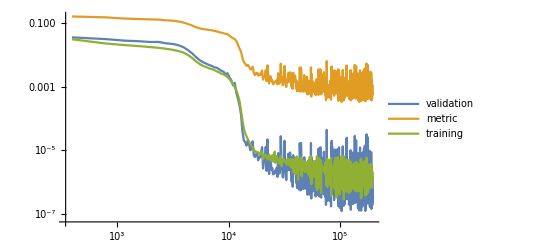

```mathematica
ListLinePlot[{validationLossList,$myMetric,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[airyTanhRMSE, airyTanhMax]
```

```mathematica
airyTanhRMSE ={}; airyTanhMax = {};
```

```mathematica
Table[{trainedTanhNet = NetTrain[tanhNet, dataAiry, ValidationSet->validationLaguerre, MaxTrainingRounds->100]; AppendTo[airyTanhRMSE,RootMeanSquare[trainedTanhNet[$refRange] - $refValues]]; AppendTo[airyTanhMax, Max[trainedTanhNet[$refRange] - $refValues]];Clear[trainedTanhNet]}, 30];
```

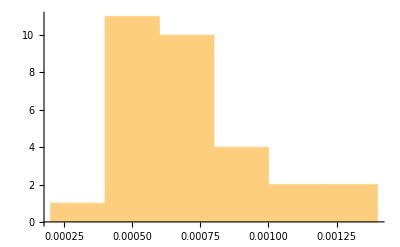

```mathematica
Histogram[airyTanhRMSE]
```

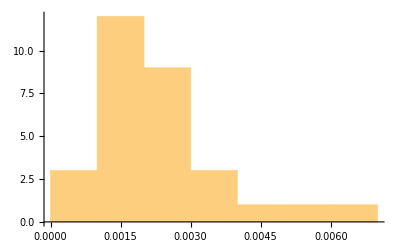

```mathematica
Histogram[airyTanhMax]
```

#### Gaussian Neural Network for Airy Function

```mathematica
gaussNet = NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^(# ^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^(#^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetric]
```

```mathematica
Clear[trainedGaussNet]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataAiry,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationAiry,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

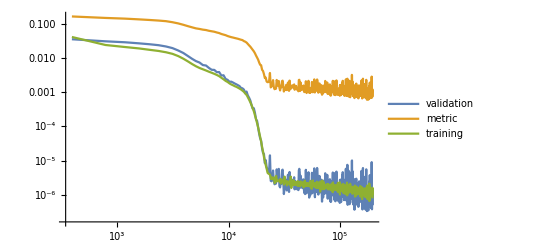

```mathematica
ListLinePlot[{validationLossListG,$myMetric,Transpose[{Range[Length[#]]*validationLossListG[[1,1]],#}& @Mean[Transpose@Partition[batchLossListG,validationLossListG[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[airyGaussRMSE, airyGaussMax]
```

```mathematica
airyGaussRMSE ={}; airyGaussMax = {};
```

```mathematica
Table[{trainedGaussNet = NetTrain[gaussNet, dataAiry, ValidationSet->validationAiry, MaxTrainingRounds->100]; AppendTo[airyGaussRMSE,RootMeanSquare[trainedGaussNet[$refRange] - $refValues]]; AppendTo[airyGaussMax, Max[trainedGaussNet[$refRange] -  $refValues]];Clear[trainedGaussNet]}, 30];
```

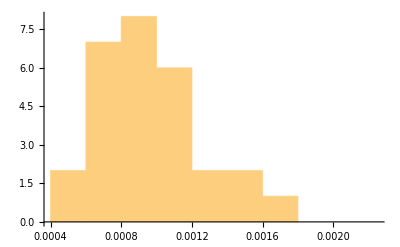

```mathematica
Histogram[airyGaussRMSE]
```

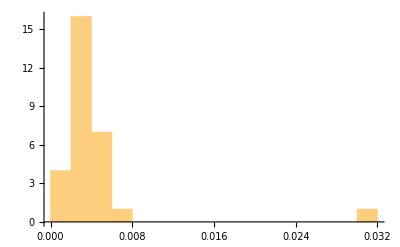

```mathematica
Histogram[airyGaussMax]
```

#### Sinusoidal Neural Network for Airy function

```mathematica
sinNet = NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSinNet]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataAiry,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationAiry,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->500,TrainingProgressFunction->{AppendTo[$myMetric,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRange] -$refValues )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

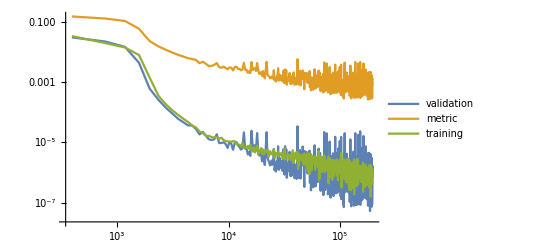

```mathematica
ListLinePlot[{validationLossListS,$myMetric,Transpose[{Range[Length[#]]*validationLossListS[[1,1]],#}& @Mean[Transpose@Partition[batchLossListS,validationLossListS[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[airySinRMSE, airySinMax]
```

```mathematica
airySinRMSE ={}; airySinMax = {};
```

```mathematica
Table[{trainedSinNet = NetTrain[sinNet, dataAiry, ValidationSet->validationAiry, MaxTrainingRounds->100]; AppendTo[airySinRMSE,RootMeanSquare[trainedSinNet[$refRange] - $refValues]]; AppendTo[airySinMax, Max[trainedSinNet[$refRange] - $refValues]];Clear[trainedSinNet]}, 30];
```

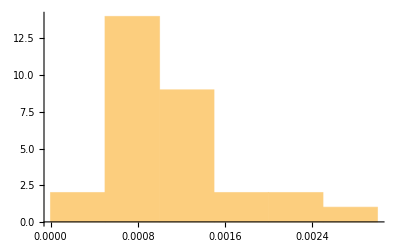

```mathematica
Histogram[airySinRMSE]
```

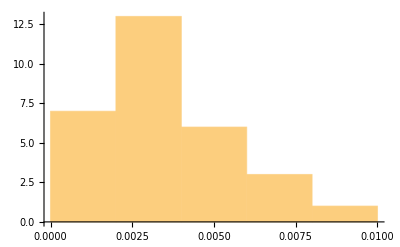

```mathematica
Histogram[airySinMax]
```

## Neural network approximation of ScorerGi[x]

### Comparison of the root mean square error (or deviation) using the following training and validation sets

#### Training and validation data

```mathematica
dataScorer = (# -> ScorerGi[#]) &@ RandomReal[{-8, 8}, 50000];
validationScorer = (# -> ScorerGi[#]) &@ RandomReal[{-8, 8}, 200];
```

#### My metric

```mathematica
$refRangeSc = Range[-8, 8, 0.001];
$refValuesSc=ScorerGi[$refRange];
```

```mathematica
$myMetricSc={};
```

#### Tanh Neural Network for ScorerGi Function

```mathematica
tanhNet = NetChain[{LinearLayer[30], Tanh, LinearLayer[20], Tanh, LinearLayer[1]}, "Input"->"Real", "Output"->NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetricSc, trainedTanhNet]
```

```mathematica
plotData[points_,color_]:=ListLinePlot[points,PlotStyle->color,FrameTicks->False,PlotRangePadding->0.1,Frame->True,PlotRange->All]
```

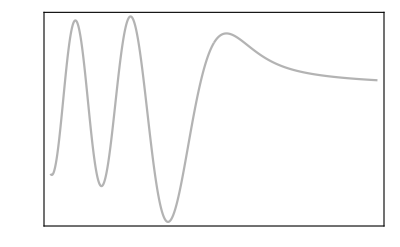

```mathematica
plot=plotData[{$refValuesSc},GrayLevel[0.7]]
```

```mathematica
plotSolution[net_,t_]:=Show[plot,plotData[net@$refRange,Red]]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->50,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

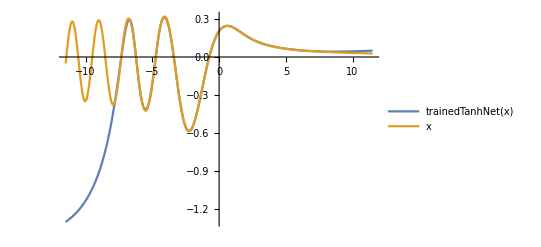

```mathematica
Plot[{trainedTanhNet[x], ScorerGi[x]}, {x, -11.5, 11.5}, PlotStyle->{"Red", "Gray"},PlotLegends->"Expressions"]
```

```mathematica
{trainedTanhNet,validationLossList,batchLossList}=NetTrain[tanhNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetricSc,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRangeSc] -$refValuesSc )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

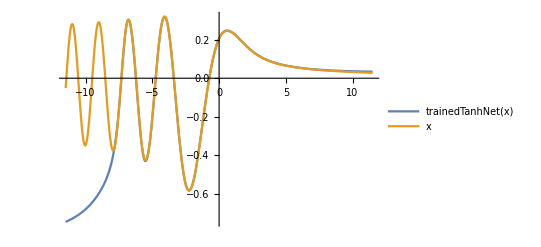

```mathematica
Plot[{trainedTanhNet[x], ScorerGi[x]}, {x, -11.5, 11.5}, PlotStyle->{"Red"},PlotLegends->"Expressions"]
```

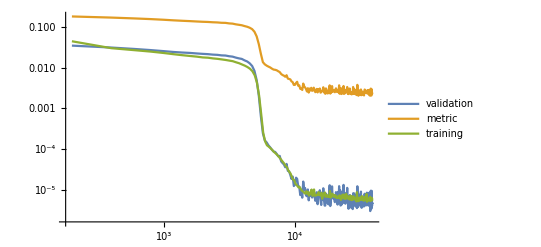

```mathematica
ListLinePlot[{validationLossList,$myMetricSc,Transpose[{Range[Length[#]]*validationLossList[[1,1]],#}& @Mean[Transpose@Partition[batchLossList,validationLossList[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[scorerTanhRMSE, scorerTanhMax]
```

```mathematica
scorerTanhRMSE ={}; scorerTanhMax = {};
```

```mathematica
Table[{trainedTanhNet = NetTrain[tanhNet, dataScorer, ValidationSet->validationScorer, MaxTrainingRounds->100]; AppendTo[scorerTanhRMSE,RootMeanSquare[trainedTanhNet[$refRangeSc] - $refValuesSc]]; AppendTo[scorerTanhMax, Max[trainedTanhNet[$refRangeSc] - $refValuesSc]];}, 20];
```

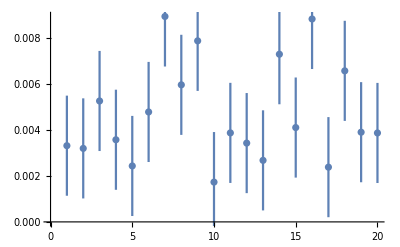

```mathematica
ErrorListPlot[Table[{scorerTanhRMSE[[i]], StandardDeviation[scorerTanhRMSE]}, {i, 1, Length[scorerTanhRMSE]}], ErrorBarFunction -> Automatic]
```

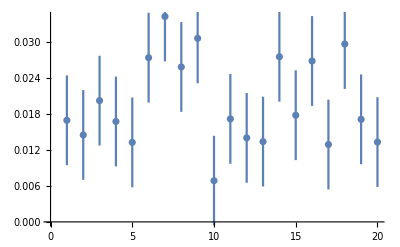

```mathematica
ErrorListPlot[Table[{scorerTanhMax[[i]], StandardDeviation[scorerTanhMax]}, {i, 1, Length[scorerTanhMax]}], ErrorBarFunction -> Automatic]
```

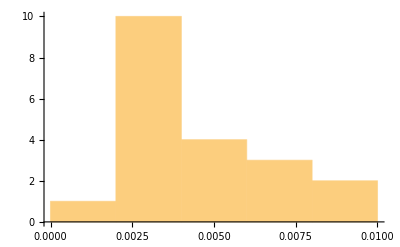

```mathematica
Histogram[scorerTanhRMSE]
```

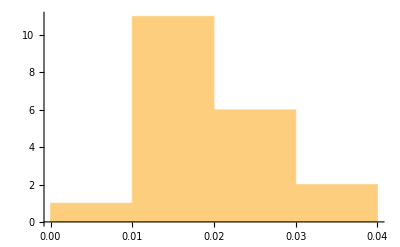

```mathematica
Histogram[scorerTanhMax]
```

#### Gaussian Neural Network for ScorerGi Function

```mathematica
gaussNet = NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^(# ^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^(#^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[$myMetricSc]
```

```mathematica
Clear[trainedGaussNet]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->50,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

Set::shape: Lists {trainedGaussNet,validationLossListG,batchLossListG} and $Aborted are not the same shape.

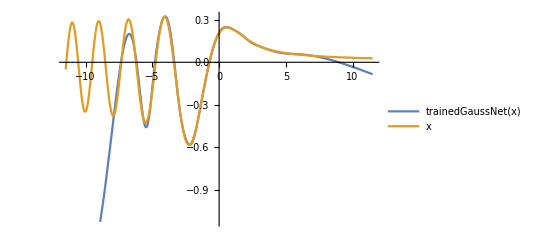

```mathematica
Plot[{trainedGaussNet[x], ScorerGi[x]}, {x, -11.5, 11.5}, PlotLegends->"Expressions"]
```

```mathematica
{trainedGaussNet,validationLossListG,batchLossListG}=NetTrain[gaussNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetricSc,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRangeSc] -$refValuesSc )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

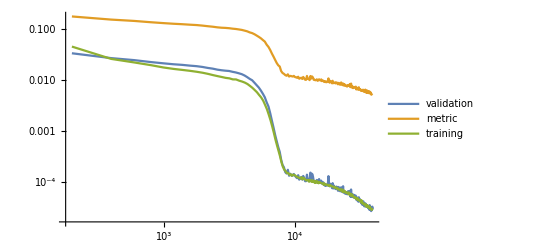

```mathematica
ListLinePlot[{validationLossListG,$myMetricSc,Transpose[{Range[Length[#]]*validationLossListG[[1,1]],#}& @Mean[Transpose@Partition[batchLossListG,validationLossListG[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[scorerGaussRMSE, scorerGaussMax]
```

```mathematica
scorerGaussRMSE ={}; scorerGaussMax = {};
```

```mathematica
Table[{trainedGaussNet = NetTrain[gaussNet, dataScorer, ValidationSet->validationScorer, MaxTrainingRounds->100]; AppendTo[scorerGaussRMSE,RootMeanSquare[trainedGaussNet[$refRange] - $refValues]]; AppendTo[scorerGaussMax, Max[trainedGaussNet[$refRange] - $refValues]];},20];
```

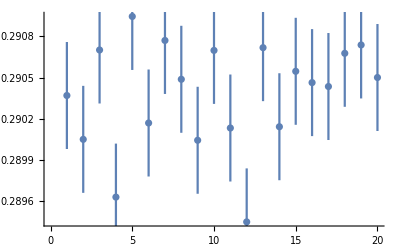

```mathematica
ErrorListPlot[Table[{scorerGaussRMSE[[i]], StandardDeviation[scorerGaussRMSE]}, {i, 1, Length[scorerGaussRMSE]}], ErrorBarFunction -> Automatic]
```

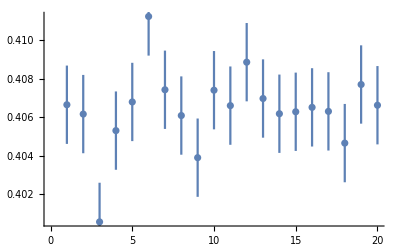

```mathematica
ErrorListPlot[Table[{scorerGaussMax[[i]], StandardDeviation[scorerGaussMax]}, {i, 1, Length[scorerGaussMax]}], ErrorBarFunction -> Automatic]
```

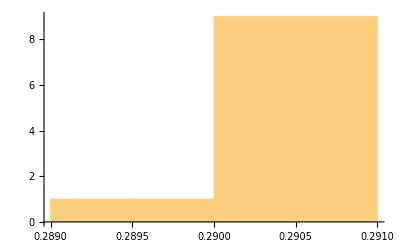

```mathematica
Histogram[scorerGaussRMSE]
```

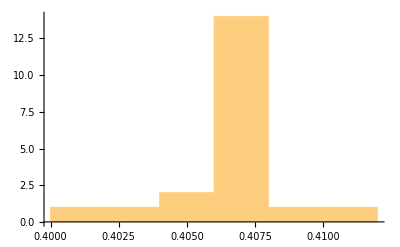

```mathematica
Histogram[scorerGaussMax]
```

#### Sinusoidal Neural Network for ScorerGi function

```mathematica
sinNet = NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
Clear[trainedSinNet]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->50,TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.5}];
```

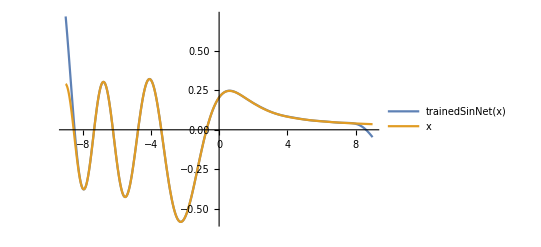

```mathematica
Plot[{trainedSinNet[x], ScorerGi[x]}, {x, -9, 9}, PlotLegends->Placed["Expressions", {0.8, 0.7}]]
```

```mathematica
{trainedSinNet,validationLossListS,batchLossListS}=NetTrain[sinNet, dataScorer,Automatic,{"TrainedNet","ValidationLossList","BatchLossList"},ValidationSet->{validationScorer,"Interval"-> Quantity[1,"Rounds"]}, MaxTrainingRounds->200,TrainingProgressFunction->{AppendTo[$myMetricSc,{#AbsoluteBatch,RootMeanSquare[(#Net[$refRangeSc] -$refValuesSc )]}]&,"Interval"-> Quantity[1,"Rounds"]}];
```

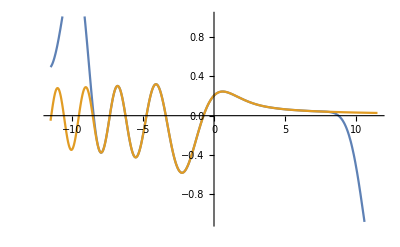

```mathematica
Plot[{trainedSinNet[x], ScorerGi[x]}, {x, -11.5, 11.5}]
```

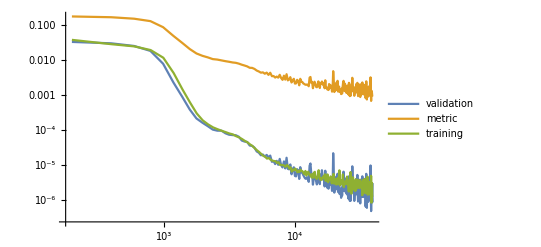

```mathematica
ListLinePlot[{validationLossListS,$myMetricSc,Transpose[{Range[Length[#]]*validationLossListS[[1,1]],#}& @Mean[Transpose@Partition[batchLossListS,validationLossListS[[1,1]]]]]},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"validation","metric","training"}]
```

```mathematica
Clear[scorerSinRMSE, scorerSinMax]
```

```mathematica
scorerSinRMSE ={}; scorerSinMax = {};
```

```mathematica
Table[{trainedSinNet = NetTrain[sinNet, dataScorer, ValidationSet->validationScorer, MaxTrainingRounds->100]; AppendTo[scorerSinRMSE,RootMeanSquare[trainedSinNet[$refRangeSc] - $refValuesSc]]; AppendTo[scorerSinMax, Max[trainedSinNet[$refRangeSc] - $refValuesSc]];}, 20];
```

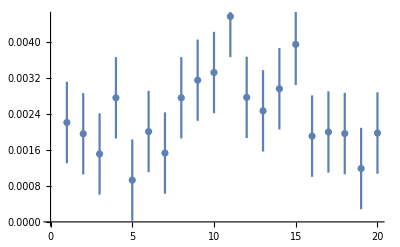

```mathematica
ErrorListPlot[Table[{scorerSinRMSE[[i]], StandardDeviation[scorerSinRMSE]}, {i, 1, Length[scorerSinRMSE]}], ErrorBarFunction -> Automatic]
```

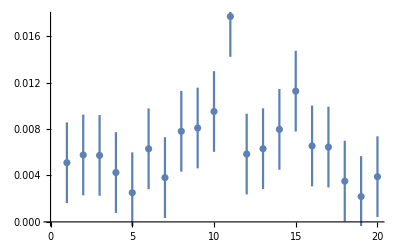

```mathematica
ErrorListPlot[Table[{scorerSinMax[[i]], StandardDeviation[scorerSinMax]}, {i, 1, Length[scorerSinMax]}], ErrorBarFunction -> Automatic]
```

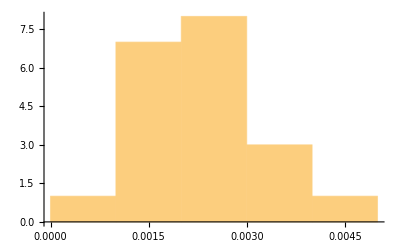

```mathematica
Histogram[scorerSinRMSE]
```

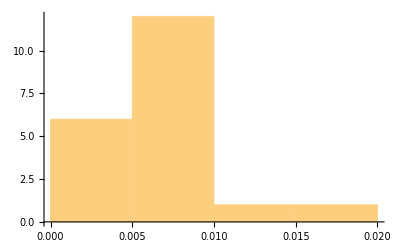

```mathematica
Histogram[scorerSinMax]
```